# THE MULTISCALE NATURE OF DEFORMATION AND METAMORPHISM

# Data, Patterns, Dynamics, Prediction

Alison Ord

Mentor: Flip Phillips

## Background

Hobbs & Ord (2015) is concerned with the processes that operate during the deformation and metamorphism of rocks in the crust and upper lithosphere of the Earth. The deformation and metamorphism of rocks involves structural rearrangements of elements of the rock at the microscale by processes such as mass diffusion, dislocation slip and climb, grain-boundary migration and fracturing at the same time as chemical reactions proceed. In some instances infiltrating fluids introduce or remove chemical components and may influence mechanical properties through changes in mineralogical composition, fluid pressure or temperature. At the same time, heat is added to or removed from the system depending on the surrounding tectonic environment. Such mechanisms do not operate independently of each other but are coupled so that each process has feedback influences on the others leading to structures and mineral assemblages that do not develop in the uncoupled environment.

Its contents are represented by this Word Cloud.

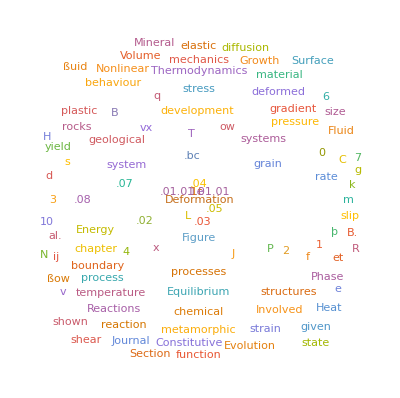

This computational essay is a first step towards developing the application of the tools of nonlinear dynamics to measuring rocks, to measuring the structural architectures which result from processes interacting and developing in a coupled environment.

## Vision

The vision for Mathematica is of moving a cursor through (x,y,z) coordinates for the surface of a deformed, folded rock and to watch data driven analyses change in different windows including: spatial attractors, wavelet transforms, singularity spectra, Hurst exponents, recurrence plots (including the ability for cross—and joint—recurrence plots and their quantitative analysis), Fourier transforms, recurrence histograms, networks, and sparsely determined nonlinear determinations of the differential equations describing the data.

## Step 1

Are folded rocks a snapshot of a nonlinear dynamic system? When layered rocks are shortened during tectonic events, the most obvious structures formed are folds. Folding of layered rocks causes a change in geological structure that can lead to a fundamental modification of the mechanical and hydraulic properties of the rock mass across several orders of magnitude in length—typically from the millimetre to the kilometre-scale.

The understanding of how, why and on which scale folding occurs therefore has fundamental implications for problems in geology and engineering, including prediction of the form and location of hydrocarbon accumulations, salt domes, groundwater flow, mineralization, and rock slope stability.

We have prepared three dimensional models of natural fold systems using photogrammetry and we explore the multifractal geometry using wavelet transforms and recurrence quantification in order to delineate the dynamics of naturally folded systems.

## The Data

```mathematica
rule30=Accumulate[(-1.)^CellularAutomaton[30,{{1},0},{1262,{{0}}}]];
```

```mathematica
Dimensions[rule30]
```

{1263}

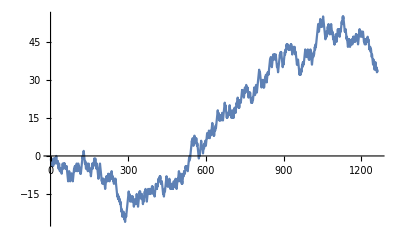

```mathematica
ListLinePlot[rule30]
```

## The Analyses

### Spatial attractors

An attractor is a stable stationary state of a system. The attractor can be a critical point, a limit cycle, a torus or a strange attractor. The term strange means that the attractor has a fractal geometry and its geometry is sensitive to initial conditions.

Here we show the spatial attractor for the data with a lag of 20, in various styles. The lag is the delay, in what is traditionally a time series, between the first column (t_0=0), the second column (t_1=t_0+lag), and successive columns (t_i=t_0+(lag*i)).

-Graphics3D-

-Graphics3D-

### Wavelet transforms

If the geometry of an object is characterised by a single fractal dimension, D, then it is called a monofractal. Some geometries are characterised by two values of D and these are called bifractals. However, if the geometry is characterised by different values of D at different points then the geometry is clearly more complicated and is called a multifractal; a spectrum of D values arises. A multifractal therefore consists of a set of interwoven fractals and is characterised by a spectrum of singularity measures.

Methods of multifractal analysis based on the wavelet transform are particularly applicable to self-similar, intermittent data sets where the wavelet acts as a 'microscope' that can zoom into the details of the signal and define local structure and singularities.

```mathematica
cwd=ContinuousWaveletTransform[rule30,WaveletScale->1];
```

```mathematica
recwd=Re@cwd[All,"Values"];
```

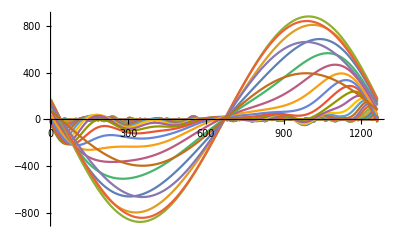

```mathematica
ListLinePlot[recwd,PlotRange->All]
```

```mathematica
cf[x_]:=Blend[{RGBColor[0., 0., 0.3],RGBColor[0., 0., 0.5],RGBColor[0, 0.1, 0.5],RGBColor[0, 0.2, 1],RGBColor[0, 0.5, 1],RGBColor[0.2, 0.7, 1],RGBColor[0.5, 0.8, 1],RGBColor[0.5, 0.9, 0.9],RGBColor[0.5, 1., 0.9],RGBColor[0.7, 1, 0.7],RGBColor[0.8, 1, 0.5],RGBColor[1, 1, 0],RGBColor[1, 0.8, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.25, 0],RGBColor[1, 0.1, 0.],RGBColor[1, 0., 0.],RGBColor[0.9, 0., 0.],RGBColor[0.8, 0., 0.],RGBColor[0.5, 0., 0.],RGBColor[0.25, 0., 0.],RGBColor[0.1, 0, 0]},x]
```

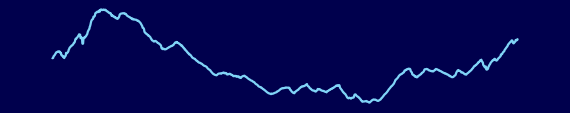
-Graphics-
-Graphics-

```mathematica
Column[{ListLinePlot[,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[recwd,ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

### Singularity spectra

The spectrum of singularity measures, the singularity spectra, describing a set of interwoven fractals are presently created using Last Wave. See Bacry et al. (1993) and Arneodo et al. (2008).

-Graphics-

### Recurrence quantitative analysis (RQA)

The goal of any nonlinear dynamical analysis of a data series is to extract features of the dynamics of the underlying physical and chemical processes that produce that spatial pattern or time series; a by-product is to characterise the signal in terms of quantitative measures.

We use recurrence plots and their quantification to extract the invariant measures of the  system including the embedding dimension, the maximum Lyapunov exponent and the entropy and characterise the system using recurrence quantification analysis (RQA).

#### Initialise

Load Flip Phillips’ RQA package:

```mathematica
Get[FileNameJoin[{ResourceFunction["NotebookRelativePath"][{"..","RQA"}],"RQA.wl"}]]
```

List the functions in the RQA package:

```mathematica
?RQA`*
```

The package is built on the equations expressed in Webber (2012) and in Webber and Marwan (2015).

#### Find and load the data

ListPlot the rule30 data:

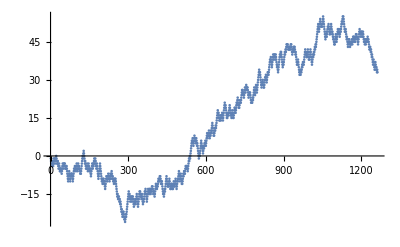

```mathematica
ListPlot[rule30]
```

Create a time series of the rule30 data:

```mathematica
ds=RQAMakeTimeSeries[rule30,1,1];
```

```mathematica
Dimensions[rule30]
```

{1263}

Display the time series:

```mathematica
ListLinePlot[ds]
```

-Graphics-

#### Estimate the lag and embedding dimensions for the data

The lag is first estimated:

```mathematica
lag=RQAEstimateLag[ds]
```

409.373

However, a lag of 10 was used in previously published work (Ord & Hobbs, 2018; Ord et al., 2018) so that is what we will use here:

```mathematica
lag=10
```

10

The embedding dimension of the system, that dimension for which the calculated fractal dimension no longer increases, is then estimated, here suggesting a dimension of 3:

```mathematica
(*RQAEstimateDimensionality[ds,lag];*)
```

Construct the embedding, which is now a list of 3 columns of data, offset by the lag of 10:

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

Display the embedding:

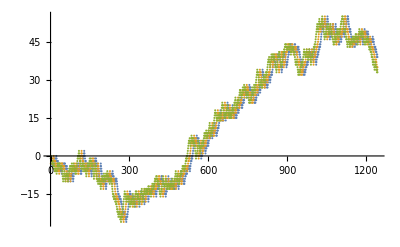

```mathematica
ListPlot[embedding]
```

#### Plot the 3D spatial attractor

Plot the attractor with axes {t,t+10,t+20}:

```mathematica
ParametricPlot3D[embedding[t],{t,1,650},SphericalRegion->True,Boxed->False]
```

-Graphics3D-

#### Calculate the distance map and the recurrence map

Webber (2012) provides explicit step-by-step details on how input vectors (data) are delayed, embedded, normed, and rescaled to define elements (distances) in the distance matrix (DM). Also described is how the recurrence matrix (RM) is derived from the DM by selecting only those recurrent points with distances falling within a selected RADIUS. Understanding of these simple examples should remove the mathematical mystery behind the basis of recurrence quantification analysis which simply finds patterns among recurrent points according to objective rules.

The radius parameter implements a cut-off limit (Heaviside function) that transforms the distance matrix (DM) into the recurrence matrix (RM). That is, all (i,j) elements in DM with distances at or below the RADIUS cutoff are included in the recurrence matrix (element value = 1), but all other elements are excluded from RM (element value = 0). Note  that the RM derives from the DM, but the two matrices are not identical.

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the distance map:

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map:

```mathematica
rm=RQARecurrenceMap[embedding];
```

The recurrence map may be plotted:

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(g↦RGBColor[1-g,g,1/2])]
```

-Graphics-

#### Time Series Epochs start here

Explore data with a window of variable size:

```mathematica
Manipulate[
ListLinePlot[Take[rule30,{x,x+w}],PlotRange->{-12.,2.}],
{{x,1},1,Length@rule30-w,1},
{{w,200},50,300,50},
SaveDefinitions->True
]
```

The following properties describe the dataset:

```mathematica
ds["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

Display the time series:

```mathematica
dsw=TimeSeriesWindow[ds,{1,Length@rule30-20}]
```

TimeSeries[…]

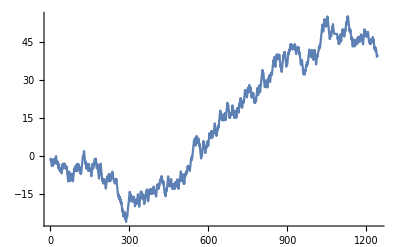

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

Compute the time series epochs for the distance map. In this example, 400 is the size of the moving window, and 200 is the number of steps by which it is moved.

```mathematica
eps=RQATimeSeriesEpochs[dsw,400,200];
```

Estimate the lag for each of the time series:

```mathematica
taus=Quiet@Map[RQAEstimateLag,eps]
```

{124.026,126.996,146.776,146.776,146.776}

Compute the mean of the lags:

```mathematica
Mean[taus]
```

138.27

Compute a list of time series for the epochs for the distance map, each of which it is possible to address and plot separately:

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps];
```

Compute the distance maps for each epoch:

```mathematica
maps=RQADistanceMap/@embeds;
```

Display the main distance map:

```mathematica
MatrixPlot[dm,]
```

-Graphics-

Since the recurrence map is calculated for each epoch, the colour ranges are slightly different from the main distance map:

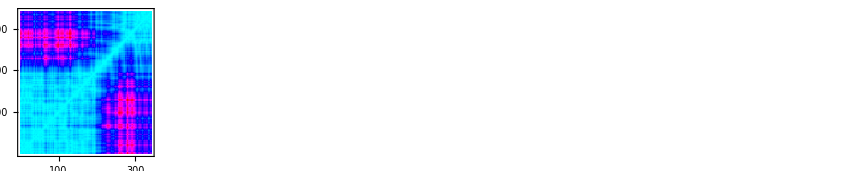

```mathematica
GraphicsGrid@{MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@maps}
```

Compute a list of time series for the epochs for the distance map, again, each of which it is possible to address and plot separately:

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

```mathematica
GraphicsGrid@{MatrixPlot[#,DataReversed->{True,False},FrameTicks->Automatic,ColorFunction->Hue]&/@numbers}
```

-Graphics-

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
TabView[{"Rec"->ListLinePlot[N[RQARecurrence/@numbers]],"Det"->ListLinePlot[N[RQADeterminism/@numbers]],"Lam"->ListLinePlot[N[RQALaminarity/@numbers]],"Trap"->ListLinePlot[N[RQATrappingTime/@numbers]],"Trend"->ListLinePlot[N[RQATrend/@numbers]],"Entropy"->ListLinePlot[N[RQAEntropy/@numbers]],"Dmax"->ListLinePlot[N[RQADmax/@numbers]],"Vmax"->ListLinePlot[N[RQAVmax/@numbers]],"Chaos"->ListLinePlot[N[RQAChaos/@numbers]]}]
```

General::munfl: Exp[-1009.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1237.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.095] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

123456789

Measures used in recurrence quantification analysis (RQA). 
 Recurrence rate  Recurrent points falling within a given radius for the number of points in signal. 
 Determinism Recurrent points forming diagonal line structures; Predictability of the system 
 Laminarity Recurrent points forming vertical line structures; intermittency of system. 
 Trapping time Average length of vertical line structures. Length of time (or space) system remains in a specific state. 
 Trend A measure of system stationarity. 
 Entropy The Shannon information entropy of probability distribution of the diagonal line lengths. Complexity of deterministic structures. 
 Dmax Length of the longest diagonal line. The shorter the line, the faster the divergence of the phase space trajectory. 
 Vmax Length of the longest vertical line. 
 Chaos 1/Dmax Interpreted to be equivalent to the maximum Lyapunov exponent of the system.

Significance of patterns in recurrence plots

-Graphics-

#### To do notes

8 July 2019
• modify the existing epoch plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch.
• Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?
•  A related problem - within the recurrence plot for all data (or at least the data you wish to explore), how do you visualise/manipulate a window representing TimeSeriesEpochs moving up and down the line of identity (LOI) of the main distance plot with the distance plot representing the epoch showing up on the side?
•  How do you do all this for 2D? 3D?

## Future Work

There remains much to be done to scale up the tools to explore two dimensional and three dimensional data, as well as thoroughly and efficiently to explore lots of data, for example multielement data derived every 1mm or less from  multispectral scanning of many kilometres of drill core.

### Discovery of physics from data

Brunton et al. (2015) note: The ability to discover physical laws and governing equations from data is one of humankind’s greatest intellectual achievements.

Discovering the physical laws and governing equations for the deformation of rocks from data obtained from deformed rocks has been a personal goal for at least 25 years (Ord, 1994). Brunton and co-workers have shown a way towards this goal. Publications in this research area have increased rapidly in the past few years, some describing successful engineering applications. Brunton et al. (2019) are now investigating the role that machine learning may in augmenting such research in the field of fluid mechanics, and in linking data with modeling, experiments, and simulations.

I would like to help drive the research in this direction for geological applications supported by the Wolfram Language.

#### Application of Brunton’s Matlab SINDy code using Octave

Brunton’s open source MATLAB code for SINDy is available at https://faculty.washington.edu/kutz/page26/

I modified this code for the open source programming software Octave https://www.gnu.org/software/octave/, tested it on the fully chaotic Lorenz system and the results published by Brunton et al. (2015, 2016), and applied it to  and obtained the following identified system (AGCC Ord&Hobbs presentation 2018)

ẋ ==0-0.12 x+0.15 y-0.03 z                 
ẏ==0 -0.04 x+0.05 y-0.09 z             
ż==0-0.07 x y-0.05 x z+0.05 x x+2.5 x+0.03 y z+0.03 y y-7.2 y+4.8 z

and attractors.

-Graphics-

-Graphics-

Programming this approach within the Wolfram Language has  high priority, together with the wavelet transform modulus maxima (WTMM) for wavelet based multifractal analysis (Bacry, 1993; Arneodo et al., 2008).

## Acknowledgments

I thank Flip Phillips and Paul Abbott for supporting my tentative steps towards incorporating the tools of nonlinear dynamics into Wolfram Language for creative application to understanding how rocks deform. I thank Stephen Wolfram and the Wolfram Summer School community, including mentors, staff, TA’s, and of course my fellow students for an intense, productive and very happy 3 weeks.

## References

Arneodo A, Audit B, Kestener P, Roux S. 2008 Wavelet-based multifractal analysis. Scholarpedia 3, 4103. (doi:10.4249/scholarpedia.4103)

Bacry E, Muzy JF, Arneodo A. 1993 Singularity spectrum of fractal signals from wavelet analysis: exact results. J. Stat. Phys. 70, 635–674. (doi:10.1007/BF01053588)

Brunton, S.L., Proctor, J.L., Kutz, J.N. 2015. Discovering governing equations from data: Sparse identification of nonlinear dynamical systems. (arXiv:1509.03580v1)

Brunton, S.L., Proctor, J.L., Kutz, J.N. 2016. Discovering governing equations from data by sparse identification of nonlinear dynamical systems. Proc. Natl. Acad. Sci. 113, 3932-3937 and Supporting Information. (doi: 10.1073/pnas.1517384113)

Brunton, S.L., Noack, B.R., Koumoutsakos, P. 2019. Machine learning for fluid mechanics. (arXiv:1905.11075v1)

Champion, K., Zheng, P., Aravkin, A.Y., Brunton, S.L., Kutz, J.N. 2019 A unified sparse optimization framework to learn parsimonious physics-informed models from data. (arXiv:1906.10612v1)

da Silva, B., Higdon, D.M., Brunton, S.L.,  Kutz, J.N. 2019 Discovery of physics from data:Universal laws and discrepancy models. (arXiv:1906.07906v1)

Hobbs BE, Ord A. 2015 Structural geology: the mechanics of deforming metamorphic rocks. Amsterdam, The Netherlands: Elsevier. (doi: 10.1016/C2012-0-01215-X)

Hobbs, B.E., Ord, A. Nonlinear dynamical analysis of GNSS data: Quantification, precursors and synchronisation. Progress in Earth and Planetary Science. 2018. (doi:10.1186/s40645-018-0193-6)

Kononov E. 2006 VRA Visual Recurrence Analysis. Version 4.9. See http://web.archive.org/web/20070131023353 and http://www.myjavaserver.com/~nonlinear/vra/download.html.

Oberst, S., Niven, R.K., Lester, D.R., Ord, A., Hobbs, B. and Hoffmann, N. Detection of unstable periodic orbits in mineralising geological systems. Chaos 28, 085711 (2018) (doi: 10.1063/1.5024134)

Ord A. 1994 The fractal geometry of patterned structures in numerical models for rock deformation. In Fractals and dynamic systems in geoscience (ed. JH Krühl), pp. 131–155. Berlin, Germany: Springer. (doi: 10.1007/978-3-662-07304-9_ 11)

Ord, A. and Hobbs, B.E. Quantitative measures of deformed rocks: the links to dynamics. Journal of Structural Geology, 2018. (doi: 10.1016/j.jsg.2018.05.027)

Ord, A., Hobbs, B.E., Dering, G. and Gessner, K. Nonlinear analysis of natural folds using wavelet transforms and recurrence plots. Philosophical Transactions of the Royal Society A. 2018. (doi: 10.1098/rsta.2017.0257)

Pospelov, B., Andronov, V., Meleshchenko, R., Danchenko, Y., Artemenko, I., Romanlak, M., Khmyrova, A., Butenko, T. 2019. Construction of methods for computing recurrence plots in space with a scalar product. Eastern-European Journal of Enterprise Technologies ISSN 1729-3774 3/4 ( 99 )  (doi: 10.15587/1729-4061.2019.169887)

Webber Jr CL. 2012 README_2012.PDF (Introduction to Recurrence Quantification Analysis, v 14.1). See http://homepages.luc.edu/~cwebber.

Webber, C.L., Jr., Marwan, N., Editors (2015). Recurrence Quantification Analysis: Theory and Best Practices

### Presentations

See also the two presentations included in the reference directory, AGCC Hobbs&Ord presentation 2018 and AGCC Ord&Hobbs presentation 2018. They provide an overview of our research, and some early results of using SINDy. They were designed for a general geology and minerals industry audience at the 2018 Australian Geological Congress in Adelaide.